```mathematica
(*精确值*)
a=Table[{i,Sin[2 Pi (i+0.3)]},{i,0,1,0.02}];
aim=ListLinePlot[a,PlotStyle->ColorData[3,"ColorList"]];
```

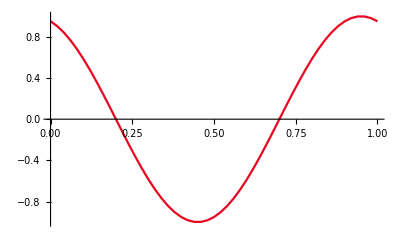
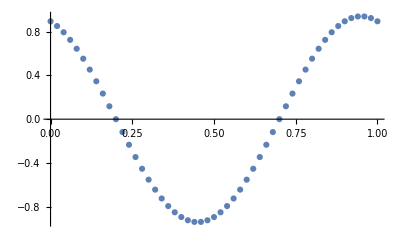
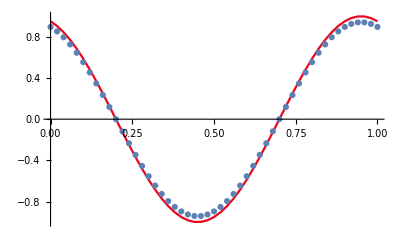

```mathematica
(*t=0.01*)
b={{0,0.896337},{0.02,0.852768},{0.04,0.795749},{0.06,0.726182},{0.08,0.645162},{0.1,0.553967},{0.12,0.454036},{0.14,0.346944},{0.16,0.234381},{0.18,0.118122},{0.2,3.46945 10^(-17)},{0.22,-0.118122},{0.24,-0.234381},{0.26,-0.346944},{0.28,-0.454036},{0.3,-0.553967},{0.32,-0.645162},{0.34,-0.726182},{0.36,-0.795749},{0.38,-0.852768},{0.4,-0.896337},{0.42,-0.925771},{0.44,-0.940605},{0.46,-0.940605},{0.48,-0.925771},{0.5,-0.896337},{0.52,-0.852768},{0.54,-0.795749},{0.56,-0.726182},{0.58,-0.645162},{0.6,-0.553967},{0.62,-0.454036},{0.64,-0.346944},{0.66,-0.234381},{0.68,-0.118122},{0.7,-1.38778 10^(-17)},{0.72,0.118122},{0.74,0.234381},{0.76,0.346944},{0.78,0.454036},{0.8,0.553967},{0.82,0.645162},{0.84,0.726182},{0.86,0.795749},{0.88,0.852768},{0.9,0.896337},{0.92,0.925771},{0.94,0.940605},{0.96,0.940605},{0.98,0.925771},{1,0.896337}};
bim=ListPlot[b];{aim,bim,Show[aim,bim]}
```

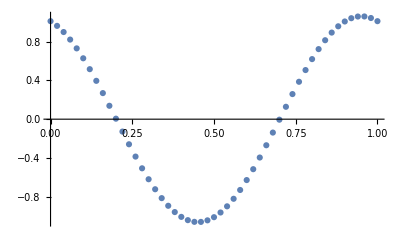
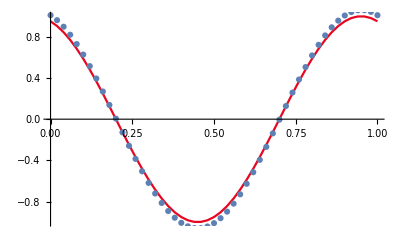
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*t=0.03*)
b={{0,1.01025},{0.02,0.96183},{0.04,0.898243},{0.06,0.82049},{0.08,0.729797},{0.1,0.627595},{0.12,0.515495},{0.14,0.395265},{0.16,0.268802},{0.18,0.1381},{0.2,0.00522024},{0.22,-0.127742},{0.24,-0.25869},{0.26,-0.385558},{0.28,-0.506346},{0.3,-0.619148},{0.32,-0.722186},{0.34,-0.813835},{0.36,-0.892649},{0.38,-0.957385},{0.4,-1.00702},{0.42,-1.04078},{0.44,-1.05812},{0.46,-1.05878},{0.48,-1.04274},{0.5,-1.01025},{0.52,-0.96183},{0.54,-0.898243},{0.56,-0.82049},{0.58,-0.729797},{0.6,-0.627595},{0.62,-0.515495},{0.64,-0.395265},{0.66,-0.268802},{0.68,-0.1381},{0.7,-0.00522024},{0.72,0.127742},{0.74,0.25869},{0.76,0.385558},{0.78,0.506346},{0.8,0.619148},{0.82,0.722186},{0.84,0.813835},{0.86,0.892649},{0.88,0.957385},{0.9,1.00702},{0.92,1.04078},{0.94,1.05812},{0.96,1.05878},{0.98,1.04274},{1,1.01025}};
bim=ListPlot[b];
{aim,bim,Show[aim,bim]}
```